Fixpunkte des Micropillar Lasersystems ohne Feedback (Ν ist hier ein griechisches Nu):

```mathematica
Solve[{0==(Ν S)/(1+T)-S/τs,0==(J-Ν)/τn-(Ν S)/(1+T),0==(cs S-T)/τt},{S,Ν,T}]
```

{{S→0,Ν→J,T→0},{S→(-1+J τs)/(cs+τn),Ν→(τn+cs J τs)/((cs+τn) τs),T→(cs (-1+J τs))/(cs+τn)}}

Jacobi-Matrix:

```mathematica
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
MatrixForm[M]
```

(Ν/(1+T)-1/τs | S/(1+T) | -(S Ν)/(1+T)^2
-Ν/(1+T) | -(1+T+S τn)/(τn+T τn) | (S Ν)/(1+T)^2
cs/τt | 0 | -1/τt)

Fixpunkt x_1^* in Jacobi-Matrix einsetzen:

```mathematica
S=0;Ν=J;T=0;
MatrixForm[M]
```

(J-1/τs | 0 | 0
-J | -1/τn | 0
cs/τt | 0 | -1/τt)

Variablen S, Ν und T wieder freigeben, um zweiten Fixpunkt x_2^* einsetzen zu können:

```mathematica
S=.;Ν=.;T=.;
```

Fixpunkt x_2^* in Jacobi-Matrix einsetzen:

```mathematica
S=(τs J-1)/(cs+τn);Ν=(τn+cs τs J)/(τs(cs+τn));T=(cs ( τs J-1))/(cs+τn);
FullSimplify[MatrixForm[M]]
```

(0 | (-1+J τs)/(τn+cs J τs) | (1-J τs)/(τn τs+cs J τs^2)
-1/τs | -(J (cs+τn) τs)/(τn (τn+cs J τs)) | (-1+J τs)/(τs (τn+cs J τs))
cs/τt | 0 | -1/τt)

Bestimmung der Eigenwerte für die Parameter des Reizenstein-Experiments, da Mathematica die Eigenwerte für die allgemeine Analyse nicht berechnen kann:

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;cs=.;J=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
J=150;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J-1)/(cs+τn);Ν=(τn+cs τs J)/(τs(cs+τn));T=(cs ( τs J-1))/(cs+τn);
FullSimplify[M];
EV=Eigenvalues[M];
λ1=Part[EV,1]
λ2=Part[EV,2]
λ3=Part[EV,3]
```

-100.

-3.84482

-0.00150052

Setzen der Parameter für das Bifurkationsdiagramm λ(J):

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;cs=.;J=.;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J-1)/(cs+τn);Ν=(τn+cs τs J)/(τs(cs+τn));T=(cs ( τs J-1))/(cs+τn);
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
EV=Eigenvalues[M];
λ1=Part[EV,1];
λ2=Part[EV,2];
λ3=Part[EV,3];
```

Eigenwerte in Abhängigkeit von J:

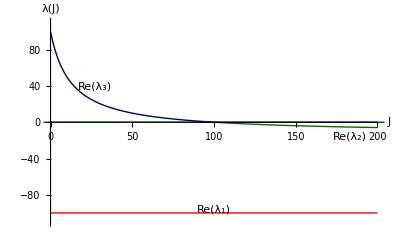

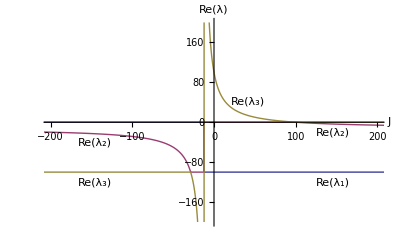

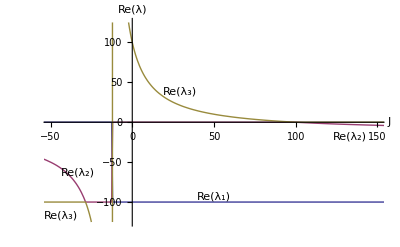

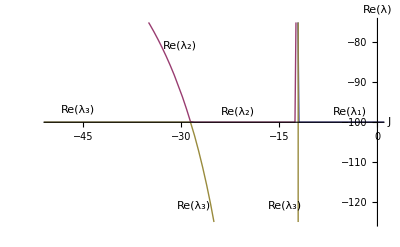

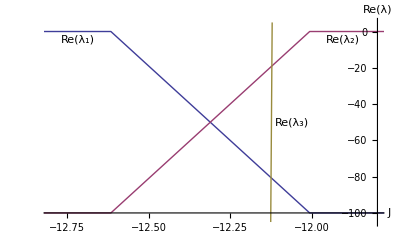

```mathematica
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J,0,200},AxesLabel->{"J","λ(J)"},PlotRange->{{0,200},{-110,110}},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]],Red,{Darker[Darker[Green]],Dashed},{Darker[Darker[Blue]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.50,.08}]],Text["Re(λ_2)",Scaled[{.90,.43}]],Text["Re(λ_3)",Scaled[{.15,.67}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J,-1000,1000},AxesOrigin->{0,0},AxesLabel->{"J","Re(λ)"},PlotRange->{{-200,200},{-200,200}},Epilog->{Text["Re(λ_1)",Scaled[{.85,.21}]],Text["Re(λ_2)",Scaled[{.15,.40}]],Text["Re(λ_2)",Scaled[{.85,.45}]],Text["Re(λ_3)",Scaled[{.15,.21}]],Text["Re(λ_3)",Scaled[{.60,.60}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J,-1000,1000},AxesOrigin->{0,0},AxesLabel->{"J","Re(λ)"},PlotRange->{{-50,150},{-125,125}},Epilog->{Text["Re(λ_1)",Scaled[{.50,.14}]],Text["Re(λ_2)",Scaled[{.90,.43}]],Text["Re(λ_2)",Scaled[{.10,.26}]],Text["Re(λ_3)",Scaled[{.05,.05}]],Text["Re(λ_3)",Scaled[{.40,.65}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J,-1000,1000},AxesOrigin->{0,-100},AxesLabel->{"J","Re(λ)"},PlotRange->{{-50,0},{-125,-75}},Epilog->{Text["Re(λ_1)",Scaled[{.90,.55}]],Text["Re(λ_2)",Scaled[{.40,.87}]],Text["Re(λ_2)",Scaled[{.57,.55}]],Text["Re(λ_3)",Scaled[{.10,.56}]],Text["Re(λ_3)",Scaled[{.44,.10}]],Text["Re(λ_3)",Scaled[{.71,.10}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{J,-1000,1000},AxesOrigin->{-11.8,-100},AxesLabel->{"J","Re(λ)"},PlotRange->{{-12.8,-11.8},{-105,5}},Epilog->{Text["Re(λ_1)",Scaled[{.10,.90}]],Text["Re(λ_2)",Scaled[{.88,.90}]],Text["Re(λ_3)",Scaled[{.73,.50}]]}]
```

Setzen der Parameter für das Bifurkationsdiagramm λ(S):

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;cs=.;J=.;
M=FullSimplify[D[{(Ν S)/(1+T)-S/τs,(J-Ν)/τn-(Ν S)/(1+T),(cs S-T)/τt},{{S,Ν,T}}]];
S=(τs J-1)/(cs+τn);Ν=(τn+cs τs J)/(τs(cs+τn));T=(cs ( τs J-1))/(cs+τn);
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
S=.;J=(S(cs+τn)+1)/τs;
EV=Eigenvalues[M];
λ1=Part[EV,1];
λ2=Part[EV,2];
λ3=Part[EV,3];
```

Eigenwerte in Abhängigkeit von S:

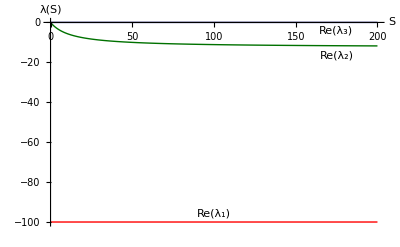

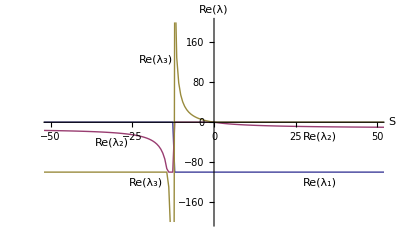

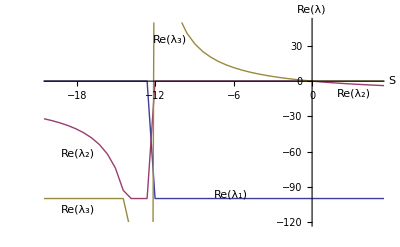

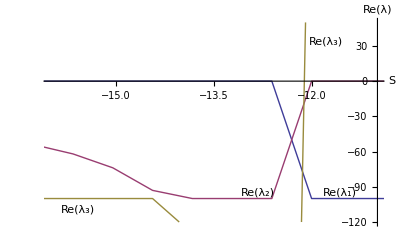

```mathematica
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,0,200},AxesLabel->{"S","λ(S)"},PlotStyle->{Red,Darker[Darker[Green]],Darker[Darker[Blue]],Red,{Darker[Darker[Green]],Dashed},{Darker[Darker[Blue]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.50,.06}]],Text["Re(λ_2)",Scaled[{.86,.82}]],Text["Re(λ_3)",Scaled[{.86,.94}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesOrigin->{0,0},AxesLabel->{"S","Re(λ)"},PlotRange->{{-50,50},{-200,200}},Epilog->{Text["Re(λ_1)",Scaled[{.81,.21}]],Text["Re(λ_2)",Scaled[{.20,.40}]],Text["Re(λ_2)",Scaled[{.81,.43}]],Text["Re(λ_3)",Scaled[{.30,.21}]],Text["Re(λ_3)",Scaled[{.33,.80}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesOrigin->{0,0},AxesLabel->{"S","Re(λ)"},PlotRange->{{-20,5},{-120,50}},Epilog->{Text["Re(λ_1)",Scaled[{.55,.15}]],Text["Re(λ_2)",Scaled[{.10,.35}]],Text["Re(λ_2)",Scaled[{.91,.64}]],Text["Re(λ_3)",Scaled[{.10,.08}]],Text["Re(λ_3)",Scaled[{.37,.90}]]}]
Plot[{Re[λ1],Re[λ2],Re[λ3]},{S,-1000,1000},AxesOrigin->{-11,0},AxesLabel->{"S","Re(λ)"},PlotRange->{{-16,-11},{-120,50}},Epilog->{Text["Re(λ_1)",Scaled[{.87,.16}]],Text["Re(λ_2)",Scaled[{.63,.16}]],Text["Re(λ_3)",Scaled[{.10,.08}]],Text["Re(λ_3)",Scaled[{.83,.89}]]}]
```

Zeitverläufe S(t), Ν(t) und T(t), Phasenraumportrait S(Ν) mit Berücksichtigung des Terms für spontane Emission:

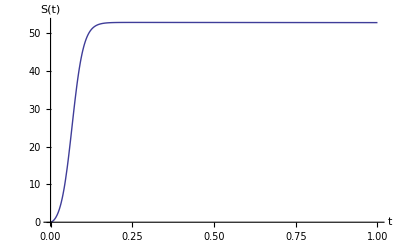

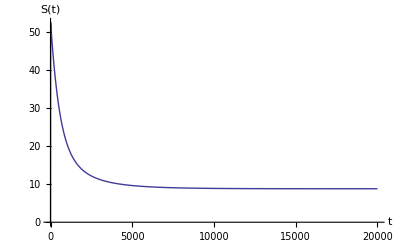

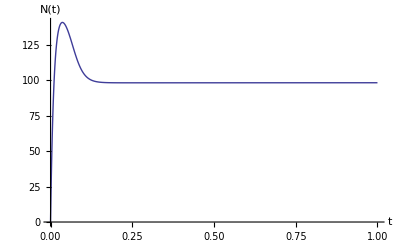

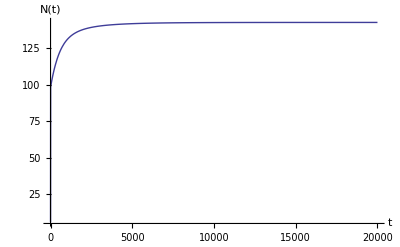

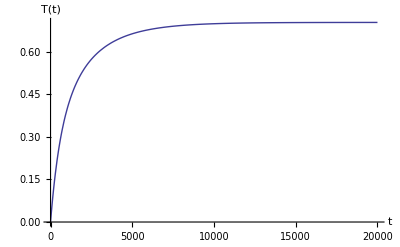

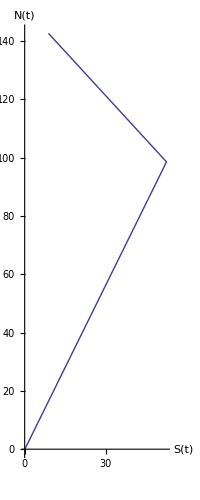

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;cs=.;J=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
J=150;
tmax=20000;
intstep=0.00001;
Sfix=(τs J-1)/(cs+τn);Νfix=(τn+cs τs J)/(τs(cs+τn));Tfix=(cs ( τs J-1))/(cs+τn);
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;

s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev,T[0]==Tfix+Tdev},{S,Ν,T},{t,0,tmax},StartingStepSize->intstep,Method->"ImplicitRungeKutta",MaxSteps->Infinity];
Plot[Evaluate[S[t]/.s],{t,0,tmax/20000},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[S[t]/.s],{t,0,tmax},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax/20000},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax},AxesLabel->{"t","N(t)"},PlotRange->All]
Plot[Evaluate[T[t]/.s],{t,0,tmax},AxesLabel->{"t","T(t)"},PlotRange->All]
ParametricPlot[Evaluate[{S[t],Ν[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)"},PlotRange->All]
```

Input-Output Kurve:

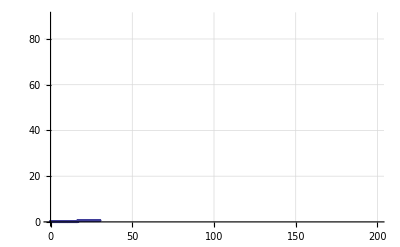

```mathematica
S=.;Ν=.;T=.;τs=.;τn=.;τt=.;β=.;cs=.;J=.;
β=0.01;
τs=10^-2;
τn=10^-2;
τt=6*10^3;
cs=0.08;
tmax=100;
Jmax=200;
iostep=0.1;
intstep=0.01;
Sfix=0.01;Νfix=J;Tfix=0;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
Tdev=-Tfix;
a=Range[0];

ProgressIndicator[Dynamic[J],{0,Jmax}]
Do[s=NDSolve[{S'[t]==(Ν[t] S[t])/(1+T[t])-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J-Ν[t])/τn-(Ν[t] S[t])/(1+T[t]),T'[t]==(cs S[t]-T[t])/τt,S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev,T[0]==Tfix+Tdev},{S,Ν,T},{t,0,tmax},StartingStepSize->intstep,Method->"ImplicitRungeKutta",MaxSteps->Infinity];a=Flatten[Append[a,{J,Evaluate[S[tmax]/.s]}]],{J,0,Jmax,iostep}];
io=Partition[a,2];
ListPlot[io,AxesLabel->{"J","S(J)"},PlotMarkers->{●,3},GridLines->Automatic]
```